# A Mathematica NURBS (Non-Uniform Rational B-Splines) Package and Its Applications

Author: Liutong Zhou
Columbia University

## Chapter 2 B-Spline Basis Functions

All the customized functions we showed here are included in the package “NURBS”

```mathematica
Needs["NURBS`"]
```

Package NURBS.wl By Liutong Zhou, Version 1.0
Created on Nov. 25 2016
Last Updated on Dec 11 2016

User-accessible functions:
NDegreePowerBasis,Bernstein, MyBezierCurve, PlotBezierCurve, RationalBezierCurve, PlotRationalBezierCurve,BezierSurface,PlotBezierSurface,
RationalBezierSurface,PlotRationalBezierSurface, MyBSplineBasis, 

Type ?functionname to see usage information

## 2.2 Definition of B-Spline Basis Functions

Let U={u_0,...,u_m} be a nondecreasing sequence of real numbers. The u_is are called knots and U is called the knot vector. The i-th B-Spline Basis function of p-degree, denoted by N_(i,p)(u) is defined by recurrence (2.5) in the NURBS Book.

N_(i,0)(u)=Piecewise[{{1, if u_i≤u<u_(i+1)}, {0, otherwise}}], for 0≤i≤m-1
N_(i,p)(u)=(u-u_i)/(u_(i+p)-u_i)N_(i,p-1)(u)+(u_(i+p+1)-u)/(u_(i+p+1)-u_(i+1))N_(i+1,p-1)(u)

B-Spline Basis Function is calculate by MyBSplineBasis[U,i,p,u] in the “NURBS” package. 

MyBSplineBasis[U,i,p,u] uses the above recurrence  to calculate B-Splines Basis, though there are better ways to implement it.

```mathematica
?MyBSplineBasis
```

MyBsplineBasis[U,i,p,u] returns the ith p degree B-Spline Basis function defined by knotvector U

### Example 1

We do the same example 2.4 as that in the NURBS Book

```mathematica
MyBSplineBasis[{0,0,0,1,2,3,4,4,5,5,5},#,2,5/2]&/@{2,3,4}
```

{1/8,3/4,1/8}

This is the same solution as that given in example 2.4. 

Mathematica also has a built-in B-Spline Basis Function, which is more powerful.

```mathematica
?BSplineBasis
```

RowBox[{"BSplineBasis", "[", RowBox[{StyleBox["d", "TI"], ",", StyleBox["x", "TI"]}], "]"}] gives the zeroth uniform B-spline basis function of degree StyleBox["d", "TI"] at StyleBox["x", "TI"].
RowBox[{"BSplineBasis", "[", RowBox[{StyleBox["d", "TI"], ",", StyleBox["n", "TI"], ",", StyleBox["x", "TI"]}], "]"}] gives the StyleBox["n", "TI"]SuperscriptBox["", "th"] uniform B-spline basis function of degree StyleBox["d", "TI"].
RowBox[{RowBox[{"BSplineBasis", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["d", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["u", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "}"}], ",", StyleBox["n", "TI"], ",", StyleBox["x", "TI"]}], "]"}], " "}] gives the StyleBox["n", "TI"]SuperscriptBox["", "th"] non-uniform B-spline basis function of degree StyleBox["d", "TI"] with knots at positions SubscriptBox[StyleBox["u", "TI"], StyleBox["i", "TI"]].

```mathematica
BSplineBasis[{2,{0,0,0,1,2,3,4,4,5,5,5}},#,5/2]&/@{2,3,4}
```

{1/8,3/4,1/8}

This is the same results we get using MyBSplineBasis

### Example 2

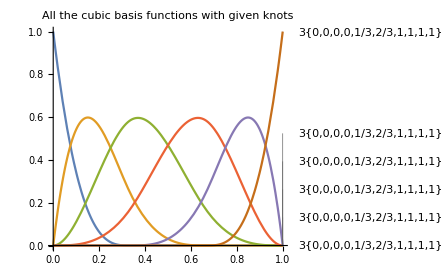

```mathematica
knots={0,0,0,0,1/3,2/3,1,1,1,1};
Plot[Evaluate[Table[BSplineBasis[{3,knots},i,x],{i,0,5}]],{x,0,1},PlotLabels->"Expressions",PlotLabel->"All the cubic basis functions with given knots",LabelStyle->Black]
```

## 2.3 Derivatives of B-Spline Basis Functions

The derivative of a basis function is given by

```mathematica
D[BSplineBasis[p,i,u],u]//TraditionalForm
```

(p+1) p-1i((p+1) u)/p-(p+1) p-1i+1((p+1) u)/p

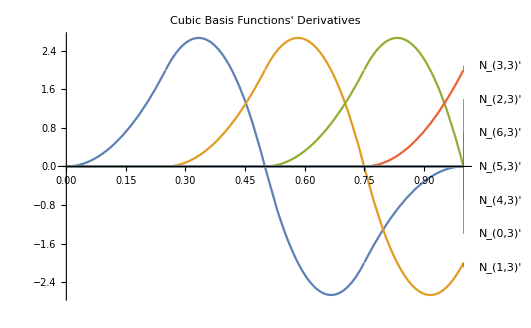

```mathematica
Plot[Evaluate@Table[D[BSplineBasis[3,i,u],u],{i,0,6}],{u,0,1},PlotRange->Full,PlotLabels->Table[Subscript[N, i,3]',{i,0,6}],LabelStyle->Black,PlotLabel->"Cubic Basis Functions' Derivatives"]
```

Equation (2.10) and (2.11) in the NURBS Book give the k-th derivative of N_(i,p)(u)